```mathematica
elcdm[z_]=√(om (1+z)^3+1-om);
```

```mathematica
elinear[z_] = Sqrt[om(1+z)^3 + (1- om)(1+z)^(3(1+w0linear - w1linear)) Exp[3 w1linear z]];
```

```mathematica
elinder[z_] = Sqrt[om(1+z)^3 + (1-om)(1+z)^(3(1 + w0linder + w1linder))Exp[3 w1linder (1/(1+z) - 1)]];
```

```mathematica
eode[z_] = Sqrt[om (1+z)^3 + a1 Cos[a2 z^2 + a3] + (1 - a1 Cos[a3] - om)];
```

```mathematica
q[z_, e_]:= -1 + (1+z)e'[z]/e[z]
```

```mathematica
qLCDM= q[z, elcdm];
```

```mathematica
qLinear = q[z, elinear];
```

```mathematica
qLinder = q[z, elinder];
```

```mathematica
qOA = q[z, eode];
```

```mathematica
om = 0.3;
w0linear = -1.25;
w1linear = 1.97;
w0linder=-1.29;
w1linder= 2.84;
a1 = -3.36;
a2= 2.12;
a3 = -0.06 Pi;
```

```mathematica
ploteLCDM = Plot[elcdm[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"ΛCDM"];
```

```mathematica
ploteLinear = Plot[elinear[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"Linear"];
```

```mathematica
ploteLinder = Plot[elinder[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"Linder"];
```

```mathematica
ploteOA = Plot[eode[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"OA"];
```

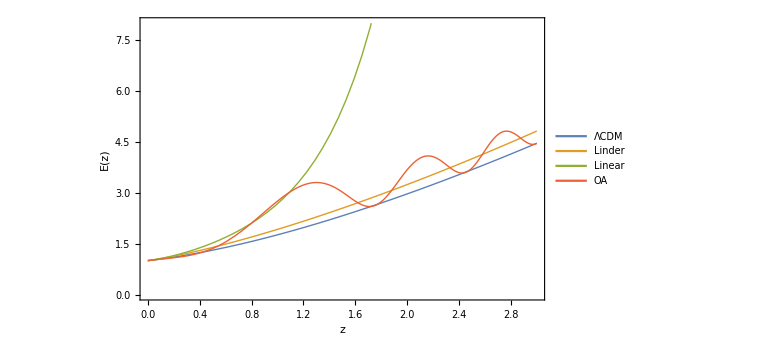

```mathematica
graficoE=Plot[{elcdm[z], elinder[z], elinear[z], eode[z]}, {z, 0, 3}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["E(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], PlotRange->{0,8}, LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"ΛCDM", "Linder", "Linear", "OA"},LegendFunction->"Frame", Background->White],{Left,Top}]]
```

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\final_plots"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\final_plots

```mathematica
Export["E(z).png",graficoE,ImageResolution->700]
```

E(z).png

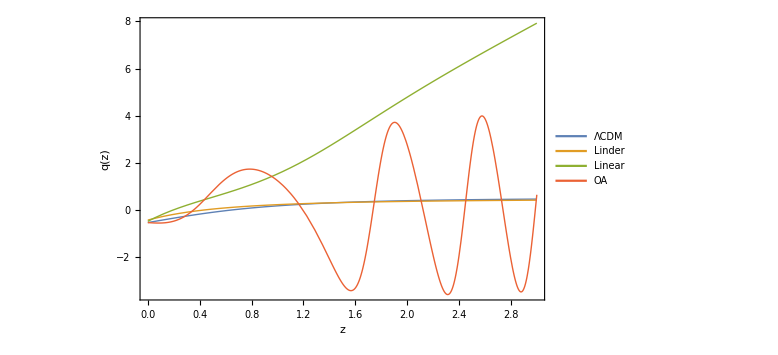

```mathematica
graficoq=Plot[{q[z, elcdm], q[z,elinder], q[z,elinear], q[z,eode]}, {z, 0, 3}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"ΛCDM", "Linder", "Linear", "OA"},LegendFunction->"Frame", Background->White],{Left,Top}]]
```

```mathematica
Export["q(z).png",graficoq,ImageResolution->700]
```

q(z).png

```mathematica
r[z_, e_]= q[z,e] (2 q[z,e] + 1) + (1+z)D[q[z,e],z];
```

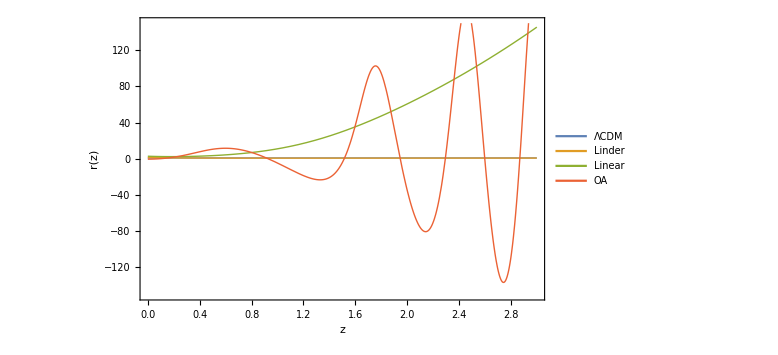

```mathematica
graficor=Plot[{r[z, elcdm], r[z,elinder], r[z,elinear], r[z,eode]}, {z, 0, 3}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["r(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], PlotRange->{-150,150}, LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"ΛCDM", "Linder", "Linear", "OA"},LegendFunction->"Frame", Background->White],{Left,Top}]]
```

```mathematica
Export["r(z).png",graficor,ImageResolution->700]
```

r(z).png

```mathematica
s[z_, e_] = (r[z,e] - 1) / (3 ((q[z, e]) - 1/2));
```

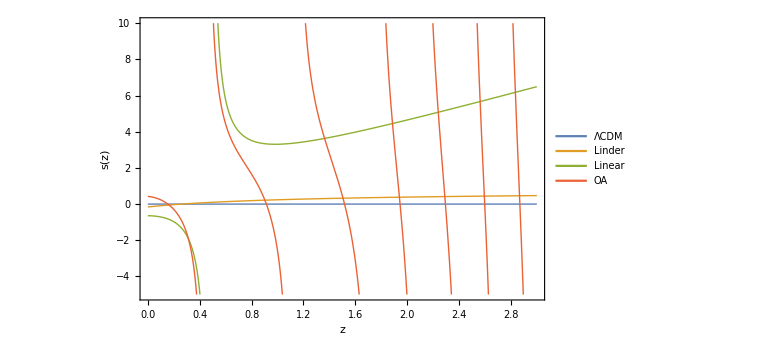

```mathematica
graficos=Plot[{s[z, elcdm], s[z,elinder], s[z,elinear], s[z,eode]}, {z, 0, 3}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["s(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], PlotRange->{-5,10}, LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"ΛCDM", "Linder", "Linear", "OA"},LegendFunction->"Frame", Background->White],{Left,Top}]]
```

```mathematica
Export["s(z).png",graficos,ImageResolution->700]
```

s(z).png

```mathematica
elcdmA[a_]=√(om/a^3+1-om);
```

```mathematica
elinearA[a_] = Sqrt[om(1/a)^3 + (1- om)(1/a)^(3(1+w0linear - w1linear)) Exp[3 w1linear (1/a - 1)]];
```

```mathematica
elinderA[a_] = Sqrt[om(1/a)^3 + (1-om)(1/a)^(3(1 + w0linder + w1linder))Exp[3 w1linder (a - 1)]];
```

```mathematica
eodeA[a_] = Sqrt[om (1/a)^3 + a1 Cos[a2 (1/a - 1)^2 + a3] + (1 - a1 Cos[a3] - om)];
```

```mathematica
slcdm = NDSolve[{d''[a] + (3/a + elcdmA'[a]/elcdmA[a])d'[a] - 3/2 om / (a^5 elcdmA[a]^2) d[a] == 0, d[0.01]== 0.0001, d'[0.01]==0.01}, d, {a, 0.01, 1}];
```

```mathematica
slinear = NDSolve[{d''[a] + (3/a + elinearA'[a]/elinearA[a])d'[a] - 3/2 om / (a^5 elinearA[a]^2) d[a] == 0, d[0.01]== 0.0001, d'[0.01]==0.01}, d, {a, 0.01, 1}];
```

```mathematica
slinder = NDSolve[{d''[a] + (3/a + elinderA'[a]/elinderA[a])d'[a] - 3/2 om / (a^5 elinderA[a]^2) d[a] == 0, d[0.01]== 0.0001, d'[0.01]==0.01}, d, {a, 0.01, 1}];
```

```mathematica
sode = NDSolve[{d''[a] + (3/a + eodeA'[a]/eodeA[a])d'[a] - 3/2 om / (a^5 eodeA[a]^2) d[a] == 0, d[0.01]== 0.0001, d'[0.01]==0.01}, d, {a, 0.01, 1}];
```

```mathematica
deltalcdm[a_]:=d[a]/.Flatten[slcdm]
```

```mathematica
deltalinear[a_]:=d[a]/.Flatten[slinear]
```

```mathematica
deltalinder[a_]:=d[a]/.Flatten[slinder]
```

```mathematica
deltaode[a_]:=d[a]/.Flatten[sode]
```

```mathematica
flcdm[a_]:=(deltalcdm'[a]*a)/deltalcdm[a]
```

```mathematica
flinear[a_] :=(deltalinear'[a]*a)/deltalinear[a]
```

```mathematica
flinder[a_]:=deltalinder'[a]/deltalinder[a]*a
```

```mathematica
fode[a_]:=deltaode'[a]/deltaode[a]*a
```

```mathematica
omegam[a_,e_]:=om/(a^3 e[a]^2)
```

```mathematica
gammalcdm[a_]:=Log[flcdm[a]]/Log[omegam[a,elcdmA]]
```

```mathematica
gammalinder[a_]:=Log[flinder[a]]/Log[omegam[a,elinderA]]
```

```mathematica
gammalinear[a_]:=Log[flinear[a]]/Log[omegam[a,elinearA]]
```

```mathematica
gammaode[a_]:= Log[fode[a]]/Log[omegam[a,eodeA]]
```

```mathematica
Plot[deltalcdm[a], {a, 0.01, 0.999}];
```

```mathematica
Plot[deltalinder[a], {a, 0.01, 0.999}];
```

```mathematica
Plot[deltalinear[a], {a, 0.01, 0.999}];
```

```mathematica
Plot[deltaode[a], {a, 0.01, 0.999}];
```

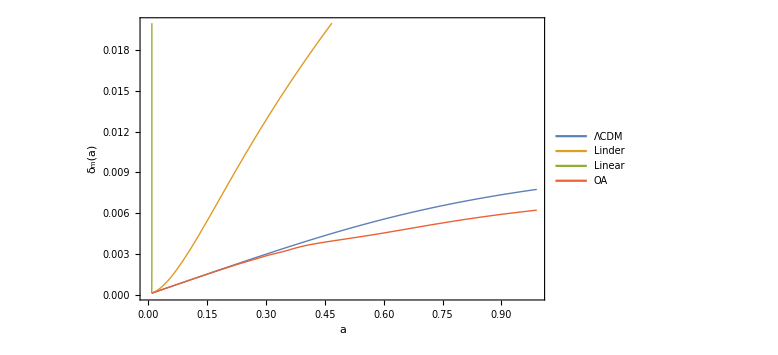

```mathematica
graficodeltam=Plot[{deltalcdm[a], deltalinder[a], deltalinear[a], deltaode[a]}, {a, 0.01, 0.99}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["a", Black, FontSize->24],Style["δ_m(a)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black],  PlotRange->{0,0.02}, LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"ΛCDM", "Linder", "Linear", "OA"},LegendFunction->"Frame", Background->White],{Right,Top}]]
```

```mathematica
Export["d_m(a).png",graficodeltam,ImageResolution->700]
```

d_m(a).png

```mathematica
Plot[flcdm[1/(1+z)], {z, 0.001, 3}];
```

```mathematica
Plot[flinder[1/(1+z)], {z, 0.001,3}];
```

```mathematica
Plot[flinear[1/(1+z)], {z, 0.001,3}];
```

```mathematica
Plot[fode[1/(1+z)], {z, 0.001,3}];
```

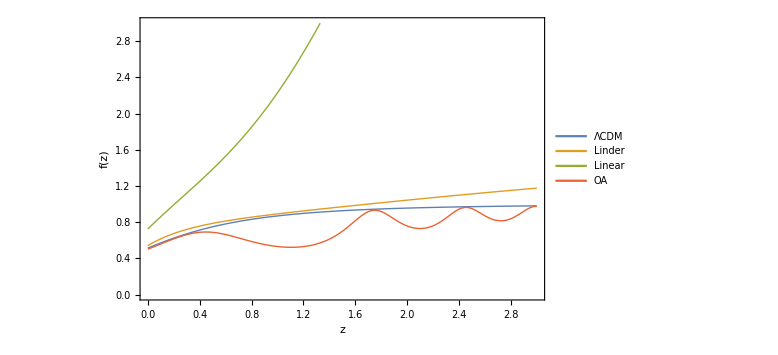

```mathematica
graficof=Plot[{flcdm[1/(1+z)], flinder[1/(1+z)], flinear[1/(1+z)], fode[1/(1+z)]}, {z, 0,3},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["f(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black],  PlotRange->{0,3}, LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"ΛCDM", "Linder", "Linear", "OA"},LegendFunction->"Frame", Background->White],{Right,Top}]]
```

```mathematica
Export["f(z).png",graficof,ImageResolution->700]
```

f(z).png

```mathematica
Plot[gammalcdm[1/(1+z)], {z, 0, 3}];
```

```mathematica
Plot[gammalinder[1/(1+z)], {z, 0, 3}];
```

```mathematica
Plot[gammalinear[1/(1+z)], {z, 0, 3}];
```

```mathematica
Plot[gammaode[1/(1+z)], {z, 0, 3}];
```

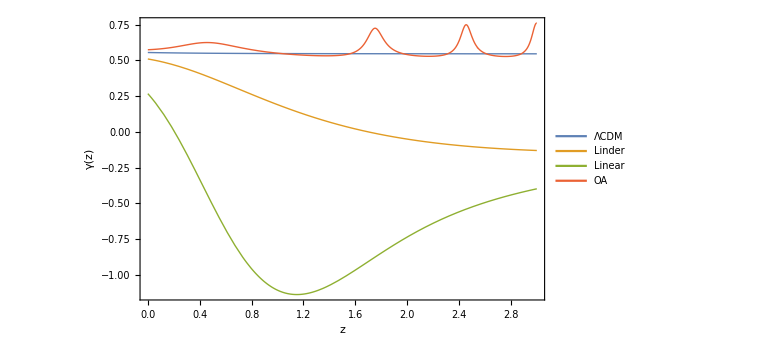

```mathematica
graficogamma=Plot[{gammalcdm[1/(1+z)], gammalinder[1/(1+z)], gammalinear[1/(1+z)], gammaode[1/(1+z)]}, {z, 0, 3},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["γ(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"ΛCDM", "Linder", "Linear", "OA"},LegendFunction->"Frame", Background->White],{Left,Bottom}]]
```

```mathematica
Export["gamma(z).png",graficogamma,ImageResolution->700]
```

gamma(z).png

```mathematica
omegade[a_,e_]:=1-omegam[a,e];
w0linear = -0.95;
w1linear = 1.97;
w0linder=-0.9;
w1linder= 0.7;
```

```mathematica
wlcdm:=-1;
dm0=0.000015;
a0=0.0001;
wlinder[a_]:=w0linder+w1linder(1-a);
wlinder[a0]
wlinear[a_]:=w0linear+w1linear((1-a)/a);
wlinear[a0]
```

-0.20007

19697.1

```mathematica
A[a_,omega_,w_,e_]:=1/a(-3w[a]-(a*w'[a])/(1+w[a])+3/2(1-w[a]*omega[a,e]));
```

```mathematica
B[a_,omega_,w_,e_]:=1/a^2(-a*w'[a]+(a*w[a]*w'[a])/(1+w[a])-1/2(1-3*w[a]*omega[a,e]));
```

```mathematica
ddeltam[a_]:=dm0/a
ddeltam0=ddeltam[a0];
```

```mathematica
deltade[a_,w_]:=(1+w)/(1-3w)*dm0
ddeltade[a_,w_]:=4 w'[a]/(1-3w)^2*dm0+(1+w)/(1-3w)*ddeltam0
deltadei=deltade[a0,wlcdm]
ddeltadei=ddeltade[a0,wlcdm]
deltadeilinear=deltade[a0,wlinear[a0]]
ddeltadeilinear=ddeltade[a0,wlinear[a0]]
deltadeilinder=deltade[a0,wlinder[a0]]
ddeltadeilinder=ddeltade[a0,wlinder[a0]]
```

0.

0.

-5.00034×10^-6

-0.0500034

7.49836×10^-6

0.0749836

```mathematica
EDOlcdm = NDSolve[{dm''[a] + 3/(2a)(1-wlcdm*omegade[a,elcdmA])dm'[a]==3/(2 a^2)(omegam[a,elcdmA]*dm[a]+omegade[a,elcdmA]*dde[a]),dde''[a]+A[a,omegade,wlcdm,elcdmA]*dde'[a]+B[a,omegade,wlcdm,elcdmA]*dde[a]==3/(2a^2)(1+wlcdm)(omegam[a,elcdmA]*dm[a]+omegade[a,elcdmA]*dde[a]), dm[a0]== dm0, dm'[a0]==ddeltam0,dde[a0]==deltadei,dde'[a0]==ddeltadei}, {dm,dde}, {a, a0, 1}];
```

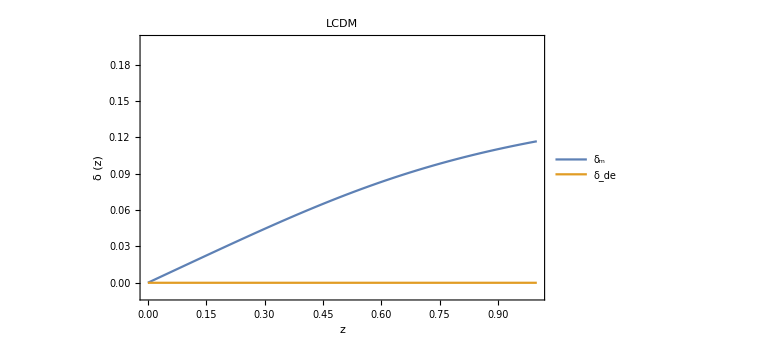

```mathematica
Plot[Evaluate[{dm[a],dde[a]}/. EDOlcdm],{a, 0.0001, 1}, ImageSize->Large,PlotStyle->Thick,PlotRange->{-0.01,0.2},PlotLegends->{"δ_m", "δ_de"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[δ"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotLabel->Style["LCDM", FontSize->18, Black]]
```

```mathematica
EDOlinder = NDSolve[{dm''[a] + 3/(2a)(1-wlinder[a]*omegade[a,elinderA])dm'[a]==3/(2 a^2)(omegam[a,elinderA]*dm[a]+omegade[a,elinderA]*dde[a]),dde''[a]+A[a,omegade,wlinder,elinderA]*dde'[a]+B[a,omegade,wlinder,elinderA]*dde[a]==3/(2a^2)(1+wlinder[a])(omegam[a,elinderA]*dm[a]+omegade[a,elinderA]*dde[a]), dm[a0]== dm0, dm'[a0]==ddeltam0,dde[a0]==deltadeilinder,dde'[a0]==ddeltadeilinder}, {dm,dde}, {a, a0, 1}];
```

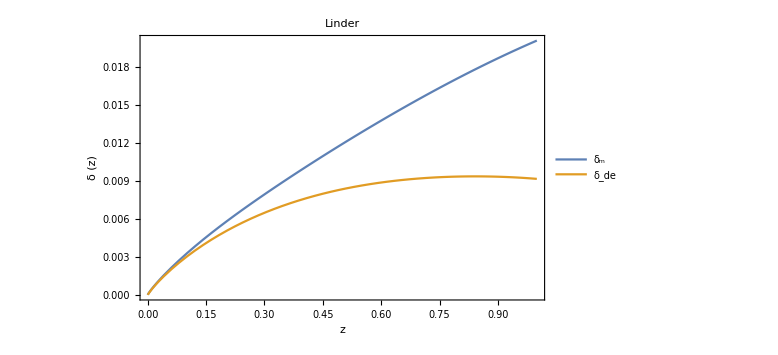

```mathematica
Plot[Evaluate[{dm[a],dde[a]}/. EDOlinder],{a, a0, 1}, ImageSize->Large,PlotStyle->Thick,PlotRange->All,PlotLegends->{"δ_m", "δ_de"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[δ"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotLabel->Style["Linder", FontSize->18, Black]]
```

```mathematica
(*EDOlinear = NDSolve[{dm''[a] + 3/(2a)(1-wlinear[a]*omegade[a,elinearA])dm'[a]==3/(2 a^2)(omegam[a,elinearA]*dm[a]+omegade[a,elinearA]*dde[a]),dde''[a]+A[a,omegade,wlinear,elinearA]*dde'[a]+B[a,omegade,wlinear,elinearA]*dde[a]==3/(2a^2)(1+wlinear[a])(omegam[a,elinearA]*dm[a]+omegade[a,elinearA]*dde[a]), dm[a0]== dm0, dm'[a0]==ddeltam0,dde[a0]==deltadeilinear,dde'[a0]==ddeltadeilinear}, {dm,dde}, {a, a0, 1}];*)
```

```mathematica
w1[a_]:=w01+b1(1-Cos[Log[1/a]])
w2[a_]:=w02+b2 Sin[Log[1/a]]
w3[a_]:=w03+b3(Sin[1/a]a-Sin[1])
```

```mathematica
w01=−1.0267;
w02=−1.0517;
w03=−1.0079;
b1=−0.2601;
b2=0.0113;
b3=0.1542;
```

```mathematica
f1[a_]:=(1/a)^(3(1+b1+w01))Exp[-3b1 Sin[Log[1/a]]]
```

```mathematica
f2[a_]:=(1/a)^(3(1+w02))Exp[3b2 (1-Cos[Log[1/a]])]
```

```mathematica
e1[a_]:=Sqrt[om/a^3+(1-om)f1[a]]
```

```mathematica
e2[a_]:=Sqrt[om/a^3+(1-om)f2[a]]
```

```mathematica
deltadei1=deltade[a0,w1[a0]]
ddeltadei1=ddeltade[a0,w1[a0]]
deltadei2=deltade[a0,w2[a0]]
ddeltadei2=ddeltade[a0,w2[a0]]
```

-1.44307×10^-6

-0.0144307

-1.78267×10^-7

-0.00178267

```mathematica
EDO1 = NDSolve[{dm''[a] + 3/(2a)(1-w1[a]*omegade[a,e1])dm'[a]==3/(2 a^2)(omegam[a,e1]*dm[a]+omegade[a,e1]*dde[a]),dde''[a]+A[a,omegade,w1,e1]*dde'[a]+B[a,omegade,w1,e1]*dde[a]==3/(2a^2)(1+w1[a])(omegam[a,e1]*dm[a]+omegade[a,e1]*dde[a]), dm[a0]== dm0, dm'[a0]==ddeltam0,dde[a0]==deltadei1,dde'[a0]==ddeltadei1}, {dm,dde}, {a, a0, 1}];
EDO2 = NDSolve[{dm''[a] + 3/(2a)(1-w2[a]*omegade[a,e2])dm'[a]==3/(2 a^2)(omegam[a,e2]*dm[a]+omegade[a,e2]*dde[a]),dde''[a]+A[a,omegade,w2,e2]*dde'[a]+B[a,omegade,w2,e2]*dde[a]==3/(2a^2)(1+w2[a])(omegam[a,e2]*dm[a]+omegade[a,e2]*dde[a]), dm[a0]== dm0, dm'[a0]==ddeltam0,dde[a0]==deltadei2,dde'[a0]==ddeltadei2}, {dm,dde}, {a, a0, 1}];
```

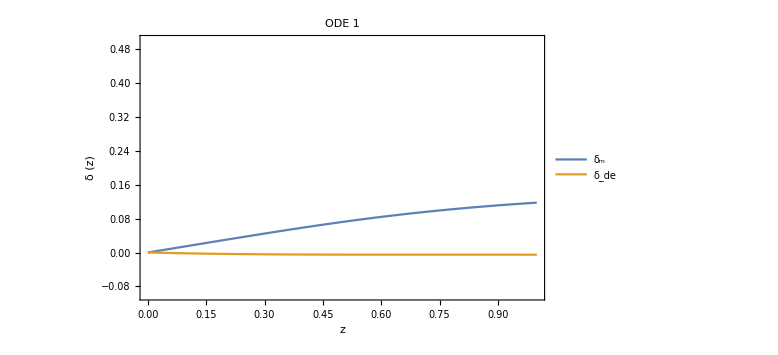

```mathematica
p1=Plot[Evaluate[{dm[a],dde[a]}/. EDO1],{a, 0.0001, 1}, ImageSize->Large,PlotStyle->Thick,PlotRange->{-0.1,0.5},PlotLegends->{"δ_m", "δ_de"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[δ"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotLabel->Style["ODE 1", FontSize->18, Black]]
```

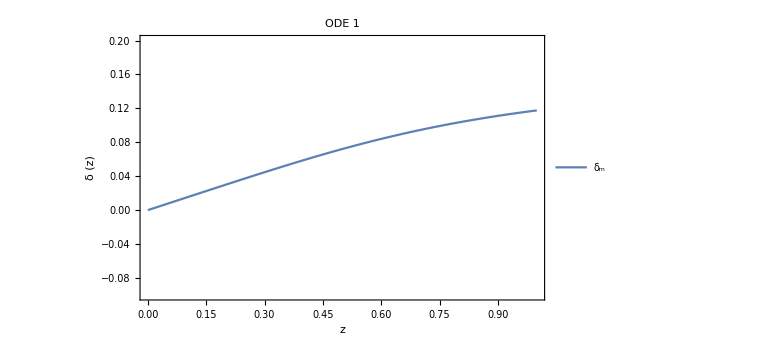

```mathematica
Plot[Evaluate[dm[a]/. EDO1],{a, 0.0001, 1}, ImageSize->Large,PlotStyle->Thick,PlotRange->{-0.1,0.2},PlotLegends->{"δ_m", "δ_de"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[δ"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotLabel->Style["ODE 1", FontSize->18, Black]]
```

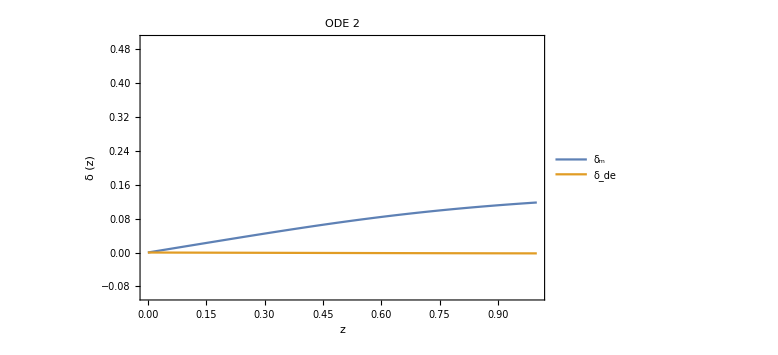

```mathematica
p2=Plot[Evaluate[{dm[a],dde[a]}/. EDO2],{a, 0.0001, 1}, ImageSize->Large,PlotStyle->Thick,PlotRange->{-0.1,0.5},PlotLegends->{"δ_m", "δ_de"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[δ"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotLabel->Style["ODE 2", FontSize->18, Black]]
```

```mathematica
dm1[a_]:=dm[a]/.Flatten[EDO1]
dde1[a_]:=dde[a]/.Flatten[EDO1]
dm2[a_]:=dm[a]/.Flatten[EDO2]
dde2[a_]:=dde[a]/.Flatten[EDO2]
```

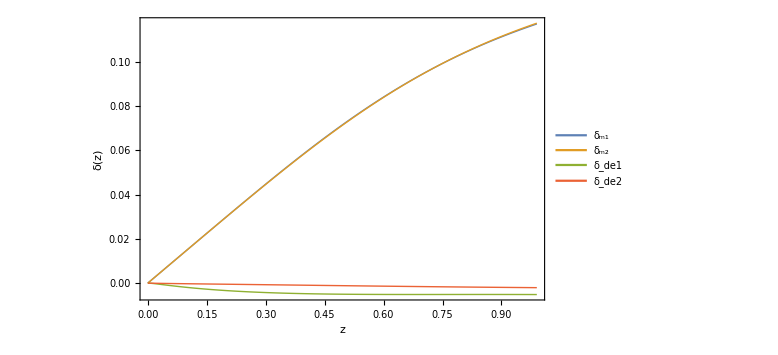

```mathematica
graficodeltacoupled=Plot[{dm1[a], dm2[a], dde1[a], dde2[a]}, {a, 0.0001, 0.99}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["δ(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"δ_m1","δ_m2", "δ_de1", "δ_de2"},LegendFunction->"Frame", Background->White],{Left,Top}]]
```

```mathematica
Export["deltacoupled(z).png",graficodeltacoupled,ImageResolution->700]
```

deltacoupled(z).png

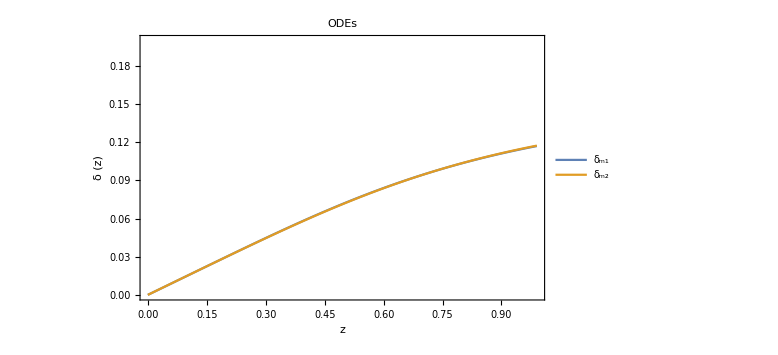

```mathematica
Plot[{dm1[a], dm2[a]}, {a, 0.0001, 0.99}, PlotStyle->Thick, ImageSize->Large, PlotRange->{-0,0.2},PlotLegends->{"δ_m1","δ_m2", "δ_de1", "δ_de2"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[δ"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotLabel->Style["ODEs", FontSize->18, Black]]
```

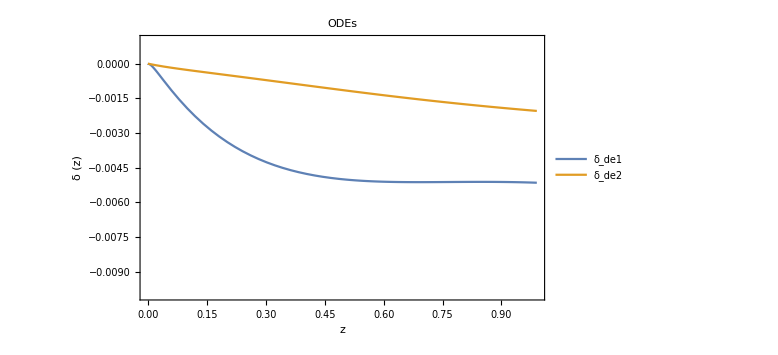

```mathematica
Plot[{dde1[a], dde2[a]}, {a, 0.0001, 0.99}, PlotStyle->Thick, ImageSize->Large, PlotRange->{-0.01,0.001},PlotLegends->{"δ_de1", "δ_de2"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[δ"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotLabel->Style["ODEs", FontSize->18, Black]]
```

```mathematica
f1Z[z_]:=(1+z)^(3(1+b1+w01))Exp[-3b1 Sin[Log[1+z]]]
```

```mathematica
eode1[z_]:=√(om(1+z)^3+(1-om)*f1Z[z]);
```

```mathematica
Plot[eode1[z],{z,0,3}];
```

```mathematica
omegamZ[z_]:=(om(1+z)^3)/elcdm[z]^2
```

```mathematica
Plot[{omegamZ[z], 1-omegamZ[z]},{z,0,3}, PlotRange->{0,1}];
```

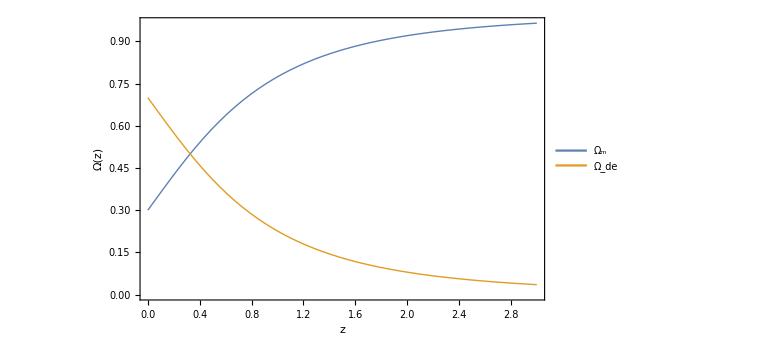

```mathematica
graficoomegamde=Plot[{omegamZ[z], 1-omegamZ[z]}, {z,0,3}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["Ω(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_m","Ω_de"},LegendFunction->"Frame", Background->White],{Left,Top}]]
```

```mathematica
Export["omega_m_de(z).png",graficoomegamde,ImageResolution->700]
```

omega_m_de(z).png

```mathematica
Plot[{omegamZ[z], 1-omegamZ[z]}, {z,0,3}, PlotStyle->Thick, ImageSize->Large, PlotRange->{0,1},PlotLegends->{Style["Ω_m", Black, FontSize->20],Style["Ω_de", Black, FontSize->20]},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[Ω"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black]]
```

```mathematica
w00=-0.942;
w22=0.531;
```

```mathematica
wodeZ[z_]:=w01+b1(1-Cos[Log[1+z]])
wode2Z[z_]:=w2[1/z]
wlinderZ[z_]:=w0linder+w1linder*(z/(1+z));
wlinearZ[z_]:=w0linear+w1linear(z);
w2[z_]:=w00+w22*z^2/(1+z^2)
```

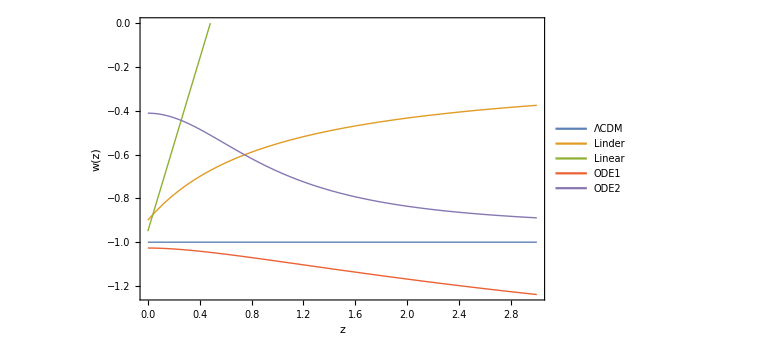

```mathematica
graficow=Plot[{w=-1, wlinderZ[z],wlinearZ[z] ,wodeZ[z], wode2Z[z]}, {z,0,3}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{ΛCDM, "Linder","Linear" ,"ODE1", "ODE2"},LegendFunction->"Frame", Background->White],{Right,Top}], PlotRange->{0,-1.5}]
```

```mathematica
Export["w(z).png",graficow,ImageResolution->700]
```

w(z).png

```mathematica
Plot[{w=-1, wlinderZ[z],wlinearZ[z] ,wodeZ[z], wode2Z[z]}, {z,0,3}, PlotStyle->Thick, ImageSize->Large, PlotRange->{-1.6,0},PlotLegends->{ΛCDM, "Linder","Linear" ,"ODE1", "ODE2"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[ω"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black]]
```

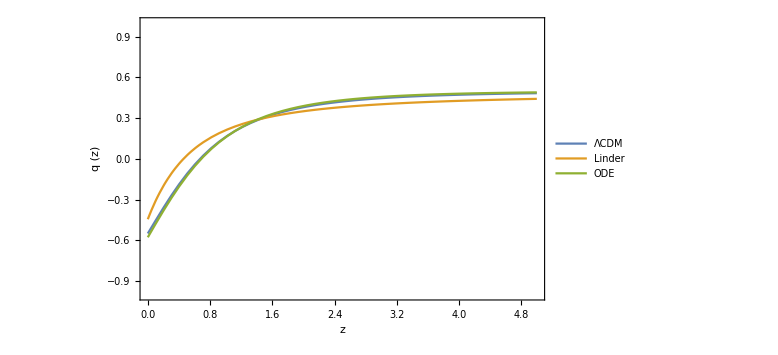

```mathematica
Plot[{q[z, elcdm], q[z, elinder], q[z, eode1]}, {z,0,5}, PlotStyle->Thick, ImageSize->Large, PlotRange->{-1,1},PlotLegends->{ΛCDM, "Linder", "ODE"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[q"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black]]
```

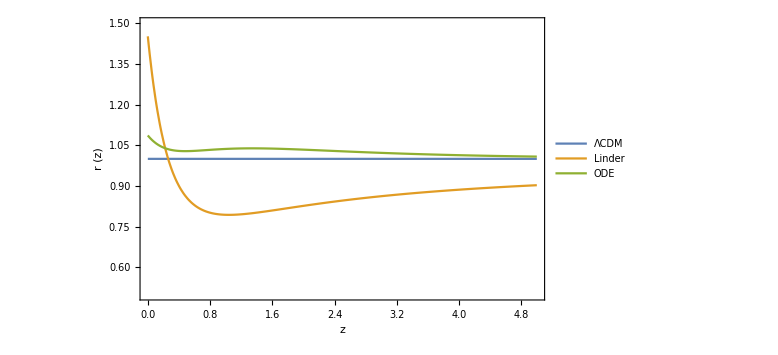

```mathematica
Plot[{r[z, elcdm], r[z, elinder], r[z, eode1]}, {z,0,5}, PlotStyle->Thick, ImageSize->Large, PlotRange->{0.5,1.5},PlotLegends->{ΛCDM, "Linder", "ODE"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[r"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black]]
```

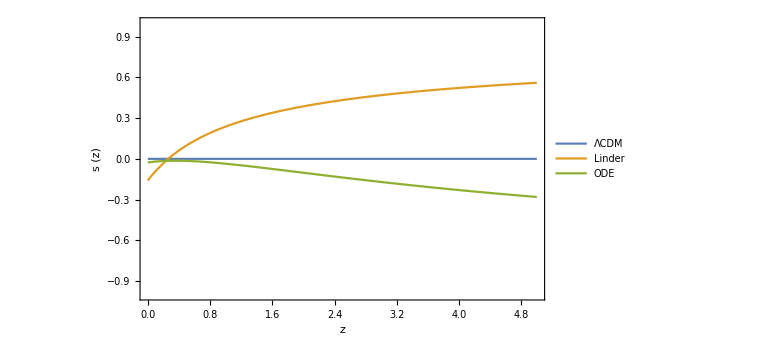

```mathematica
Plot[{s[z, elcdm], s[z, elinder], s[z, eode1]}, {z,0,5}, PlotStyle->Thick, ImageSize->Large, PlotRange->{-1,1},PlotLegends->{ΛCDM, "Linder", "ODE"},Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style[s"(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black]]
```

```mathematica
sode1 = NDSolve[{d''[a] + (3/a + e1'[a]/e1[a])d'[a] - 3/2 om / (a^5 e1[a]^2) d[a] == 0, d[0.01]== 0.0001, d'[0.01]==0.01}, d, {a, 0.01, 1}];
```

```mathematica
deltaode1[a_]:=d[a]/.Flatten[sode1]
fode1[a_]:=deltaode1'[a]/deltaode1[a]*a
```

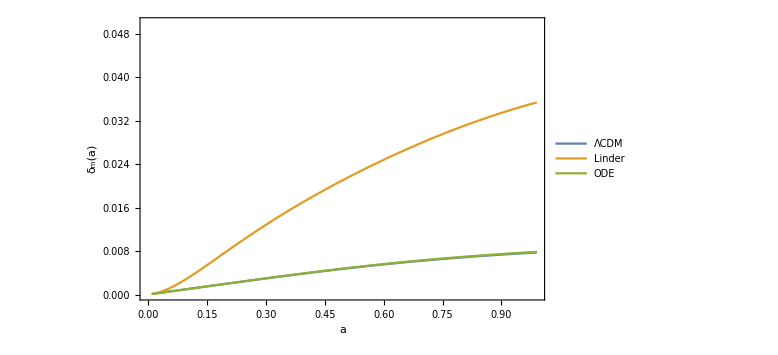

```mathematica
Plot[{deltalcdm[a], deltalinder[a], deltaode1[a]}, {a, 0.01, 0.99}, PlotLegends->{ΛCDM, "Linder", "ODE"}, Frame ->True,FrameLabel->{Style["a", Black, FontSize->20],Style["δ_m(a)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->Thick, ImageSize->Large, PlotRange->{0,0.05}]
```

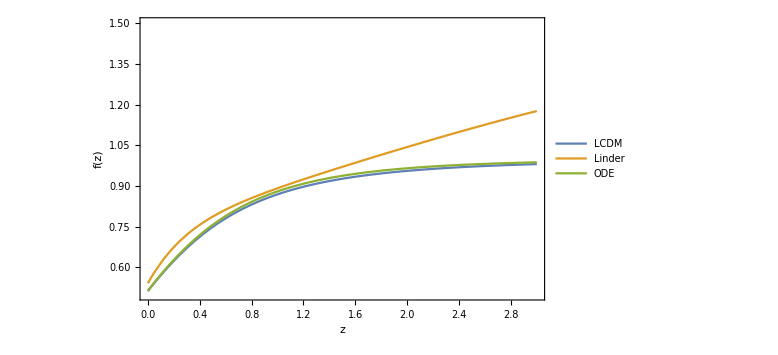

```mathematica
Plot[{flcdm[1/(1+z)], flinder[1/(1+z)], fode1[1/(1+z)]}, {z, 0,3}, PlotLegends->{"LCDM", "Linder", "ODE"}, Frame ->True,FrameLabel->{Style["z", Black, FontSize->20],Style["f(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->Thick, ImageSize->Large,PlotRange->{0.5,1.5}]
```